```mathematica
Np=2;
Id=Table[KroneckerDelta[k1,k1p],{k1,0,Np},{k1p,0,Np}];
Sx=Table[KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sy=Table[-I*KroneckerDelta[k1+1,k1p]*Sqrt[(k1+1)*(Np-k1)]+I*KroneckerDelta[k1,k1p+1]*Sqrt[(k1p+1)*(Np-k1p)],{k1,0,Np},{k1p,0,Np}];
Sz=Table[KroneckerDelta[k1,k1p]*(2*k1-Np),{k1,0,Np},{k1p,0,Np}];
ghzstate=ArrayReshape[Table[KroneckerDelta[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]];
ghzstate=N[Normalize[ghzstate]];
psi0[k1_,k2_,k3_]=(1/Sqrt[2]^(3*Np))*Sqrt[Binomial[Np,k1]*Binomial[Np,k2]*Binomial[Np,k3]];
psi1[k1_,k2_,k3_]=(1/Sqrt[Np+1])*KroneckerDelta[k1,k2]*(1/Sqrt[2]^(Np))*Sqrt[Binomial[Np,k3]];
Idbig=KroneckerProduct[Id,Id,Id];
Hamz=2*(KroneckerProduct[Sz.Sz,Id,Id]+KroneckerProduct[Id,Sz.Sz,Id]+KroneckerProduct[Id,Id,Sz.Sz])-2*(KroneckerProduct[Sz,Sz,Id]+KroneckerProduct[Sz,Id,Sz]+KroneckerProduct[Id,Sz,Sz]);
Hamx1=MatrixPower[-KroneckerProduct[Sx,Id,Id]-KroneckerProduct[Id,Sx,Id]+KroneckerProduct[Id,Id,Sx]+Np*Idbig,2];
Hamx2=MatrixPower[-KroneckerProduct[Sx,Id,Id]+KroneckerProduct[Id,Sx,Id]-KroneckerProduct[Id,Id,Sx]+Np*Idbig,2];
Hamx3=MatrixPower[KroneckerProduct[Sx,Id,Id]+KroneckerProduct[Id,Sx,Id]+KroneckerProduct[Id,Id,Sx]+Np*Idbig,2];
Hamx4=MatrixPower[KroneckerProduct[Sx,Id,Id]-KroneckerProduct[Id,Sx,Id]-KroneckerProduct[Id,Id,Sx]+Np*Idbig,2];
```

#### Try all 4 projections

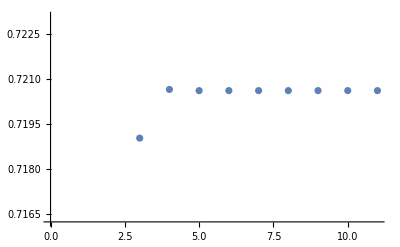

final psi={-0.274636,0,0,0,0,0,0,0,0,0,0,0,0,-0.92168,0,0,0,0,0,0,0,0,0,0,0,0,-0.274009}

ghz={0.57735,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.57735,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.57735}

0.720619

```mathematica
t=10.0;
nrounds=10;
projmatx1=MatrixExp[-Hamx1*t];
projmatx2=MatrixExp[-Hamx2*t];
projmatx3=MatrixExp[-Hamx3*t];
projmatx4=MatrixExp[-Hamx4*t];
projmatz=MatrixExp[-Hamz*t];
psi=Normalize[ArrayReshape[Table[psi0[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]]];
fidlist={Abs[Conjugate[ghzstate].psi]^2};
For[n=1,n≤nrounds,n=n+1,
psi=Normalize[projmatz.projmatx4.projmatx3.projmatx2.projmatx1.psi];
fidlist=Append[fidlist,Abs[Conjugate[ghzstate].psi]^2];
];
p1=ListPlot[fidlist];
Print[p1];
Print["final psi=",Chop[psi]];
Print["ghz=",ghzstate];
Print[Last[fidlist]];
```

#### Just one projection seems to work best

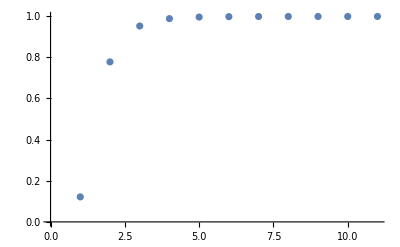

final psi={0.557317,0,0,0,0,0,0,0,0,0,0,0,0,0.615463,0,0,0,0,0,0,0,0,0,0,0,0,0.557317}

ghz={0.57735,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.57735,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.57735}

0.997746

```mathematica
t=10.0;
nrounds=10;
projmatx1=MatrixExp[-Hamx1*t];
projmatx2=MatrixExp[-Hamx2*t];
projmatx3=MatrixExp[-Hamx3*t];
projmatx4=MatrixExp[-Hamx4*t];
projmatz=MatrixExp[-Hamz*t];
psi=Normalize[ArrayReshape[Table[psi0[k1,k2,k3],{k1,0,Np},{k2,0,Np},{k3,0,Np}],{1,(Np+1)^3}][[1]]];
fidlist={Abs[Conjugate[ghzstate].psi]^2};
For[n=1,n≤nrounds,n=n+1,
psi=Normalize[projmatz.projmatx1.psi];
fidlist=Append[fidlist,Abs[Conjugate[ghzstate].psi]^2];
];
p1=ListPlot[fidlist];
Print[p1];
Print["final psi=",Chop[psi]];
Print["ghz=",ghzstate];
Print[Last[fidlist]];
```